## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedInitialSign","ConstrainedNewMethod","ConstrainedPickierFunction"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## List v0

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

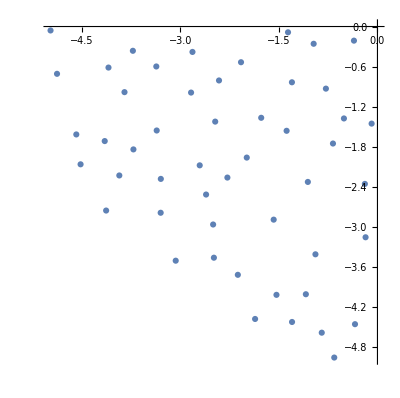

```mathematica
(* Creating list of initial Values *)
r=Random[];
listv0=Select[RandomReal[{-5,0},{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 && Norm[#]≤5)&];
listv0=Nest[removeClosest,listv0,Length[listv0]-50];
ListPlot[listv0,AspectRatio->Automatic]
```

## Function graph

```mathematica
graph[{{lineia_,dlineia_},{ lineib_,dlineib_}},tRun_,rangex_,label_]:=Block[{i,cTable,c,g0},(
i=1;
cTable=Table[
c=(lineia[p]+lineib[p])/2;
g0=Graphics[{
PointSize[0.001],
Line[{{p,lineia[p]},{p,lineib[p]}}],
If[tRun[[i,3]]=="sign",Red,
If[tRun[[i,3]]=="mag",Purple,
If[tRun[[i,3]]=="flip",Orange,Black]]
],
Point[{p,c}],
{Arrowheads->Small,Arrow[{{p-tRun[[i,1]],c},{p+tRun[[i,2]],c}}]}
}];
i=i+1;
g0
,{p,rangex}];

Show[
Plot[{lineia[x],lineib[x]},{x,rangex[[1]],rangex[[-1]]},PlotLegends->{Style["I_1(x)",FontSize->fontsize,FontFamily->Times,Italic],Style["I_2(x)",FontSize->fontsize,FontFamily->Times,Italic]},PlotLabel->Style[label,FontSize->fontsize,FontFamily->Times,Italic],
PlotRange->{{rangex[[1]],rangex[[-1]]},{0,0.7}}],
cTable,
(*,
PlotLabel->info,*)
AxesLabel->{Style["x",FontSize->fontsize,FontFamily->Times,Italic],Style["I(x)",FontSize->fontsize,FontFamily->Times,Italic]},
ImageSize->500
]
)];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"Bamboo_1","0001",r,"clean"]

(* {1,44},{1,102} arbitrary size to make the method faster *)
nx=170/r;
ny=300/r;
{ia,ib,id,io}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io}
ImageDimensions[#]&/@{ia,ib,id,io}

max=MinMax[Flatten[ImageData[id]]][[2]];
Print["max dv=", max]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45},{103,45}}

max dv=12.5952

#### Little Functions

```mathematica
pyrfi[ia_,ib_,row_,lvlmax_]:=Block[{pyrfia,pyrfib},
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ib][[row]],lvlmax];

Flatten[{pyrfia,pyrfib},{{2},{1},{3}}]
]
```

```mathematica
row=20;
lvlmin=1;
lvlmax=1;

pyrfiab=pyrfi[ia,ib,row,lvlmax];
```

## Plot: Spline interpolation Use

```mathematica
row=20;
fa1=ListInterpolation[ImageData[ia][[row]],{1,103},Method->"Spline",InterpolationOrder->1];
fb1=ListInterpolation[ImageData[ib][[row]],{1,103},Method->"Spline",InterpolationOrder->1];

fontsize=14;

tRun1=lineTest[listv0,Range[40,70],{{{fa1,fa1'},{fb1,fb1'}}},0.001,"ConstrainedNewMethod"];
tRun3=lineTest[listv0,Range[40,70],pyrfiab[[1;;1]],0.001,"ConstrainedNewMethod"];

func1={{fa1,fa1'},{fb1,fb1'}};

g1=graph[func1,tRun1,Range[40,70],"Interpolation: order 1"];
g3=graph[pyrfiab[[1;;1]][[1]],tRun3,Range[40,70],"Interpolation: order 3"];

gFinal=GraphicsRow[{g1,g3},Spacings->0,ImageSize->1300]

figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"figs"}];

Export[FileNameJoin[{figsDirectory,"splineUse.pdf"}],gFinal]
```

-Graphics-

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\splineUse.pdf